```mathematica
tf=20;
vx0=0;
vy0=.5;
x0=Pi/2;
y0=0;
sol=NDSolve[{x''[t]==Sin[y[t]-x[t]],y''[t]==-Sin[y[t]-x[t]],x'[0]==vx0,y'[0]==vy0,x[0]==x0,y[0]==y0},{x,y},{t,0,tf}];
s1= x  /. First@sol;
s2= y /. First@sol;
Animate[Show[ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}],ListLinePlot[{{Cos[s1[t]],Sin[s1[t]]},{Cos[s2[t]],Sin[s2[t]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{RGBColor[0.394, 0.394, 0.394],PointSize[.1],Point[{Cos[s1[t]],Sin[s1[t]]}]}],Graphics[{RGBColor[0.668, 0.668, 0.668],PointSize[.1],Point[{Cos[s2[t]],Sin[s2[t]]}]}]],{t,0,tf}]
```

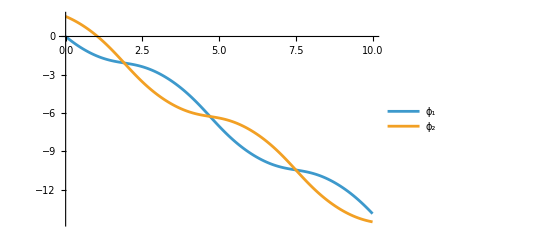

```mathematica
Show[ListLinePlot[{Legended[s1,Style["ϕ_1",12]],Legended[s2,Style["ϕ_2",12]]},PlotRange->All]]
```

```mathematica
Export["~/Desktop/Classical/Presentation Problem 2/fig3.png",Show[ListLinePlot[{Legended[s1,Style["ϕ_1",12]],Legended[s2,Style["ϕ_2",12]]},PlotRange->All,AxesLabel->{"t", "ϕ"}]],ImageResolution->300]
```

~/Desktop/Classical/Presentation Problem 2/fig3.png

```mathematica
tf=20;
s=NDSolve[{x1''[t]==Sin[x2[t]-x1[t]],x2''[t]==-Sin[x2[t]-x1[t]],x1'[0]==0.1,x2'[0]==0,x1[0]==0,x2[0]==Pi},{x1,x2},{t,0,tf}];
s11= x1  /. First@s;
s12= x2 /. First@s;
Animate[Show[ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}],ListLinePlot[{{Cos[s11[t]],Sin[s11[t]]},{Cos[s12[t]],Sin[s12[t]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{RGBColor[0.394, 0.394, 0.394],PointSize[.1],Point[{Cos[s11[t]],Sin[s11[t]]}]}],Graphics[{RGBColor[0.668, 0.668, 0.668],PointSize[.1],Point[{Cos[s12[t]],Sin[s12[t]]}]}]],{t,0,tf}]
```

```mathematica
tf=10;
vx0=0;
vy0=0;
x0=3Pi/8;
y0=Pi/8;
sol=NDSolve[{x''[t]==Sin[y[t]-x[t]],y''[t]==-Sin[y[t]-x[t]],x'[0]==vx0,y'[0]==vy0,x[0]==x0,y[0]==y0},{x,y},{t,0,tf}];
s1= x  /. First@sol;
s2= y /. First@sol;
Show[ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},Ticks->False],ParametricPlot[{.4Cos[t],.4Sin[t]},{t,0,x0},PlotStyle->{Black}],ParametricPlot[{.75Cos[t],.75Sin[t]},{t,0,y0},PlotStyle->{Black}],ListLinePlot[{{0,0},{Cos[s1[0]],Sin[s1[0]]}},PlotStyle->{Black,Dashing[{.025,.02}]}],ListLinePlot[{{0,0},{Cos[s2[0]],Sin[s2[0]]}},PlotStyle->{Black,Dashing[{.025,.02}]}],ListLinePlot[{{Cos[s1[0]],Sin[s1[0]]},{Cos[s2[0]],Sin[s2[0]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{RGBColor[0.394, 0.394, 0.394],PointSize[.1],Point[{Cos[s1[0]],Sin[s1[0]]}]}],Graphics[{RGBColor[0.668, 0.668, 0.668],PointSize[.1],Point[{Cos[s2[0]],Sin[s2[0]]}]}]]
```